## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Вспомогательные определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Утилитарные функции

```mathematica
SetAttributes[Intern,HoldAll];
Intern[x_,v_]:=(x=v)/;!ValueQ[x];
Intern[x_,v_]:=x/;ValueQ[x];
Intern[x_,v_,c_]:=(x=v)/;!ValueQ[x];
Intern[x_,v_,c_]:=If[!c[x],x,x=v]/;ValueQ[x];
```

```mathematica
SetAttributes[Cache,HoldFirst];
Cache[expr_,c_:(True&)]:=
With[{x=Extract[Unevaluated[expr],{1}]},
With[{c0=Hold[Evaluate@x]===Extract[Unevaluated[expr],{1},Hold]},
If[c0||!c0&&c[x],expr,x]
]
];
```

## Задача

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|{1,1}->0,{1,2}->0,{Even}->0,{Odd}->0,{1,3}->1,{2,3}->1|>;
thmask[Even]=<|{1,1}->1,{1,2}->1,{Even}->1,{Odd}->1,{1,3}->0,{2,3}->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f@@#1)#2)&,<|
{1,1}->LegendreP[l,Cos[u]],
{1,2}->LegendreP[l,1,Cos[u]],
{Even}->LegendreP[l,Cos[u]],
{Odd}->LegendreP[l,2,Cos[u]],
{1,3}->LegendreP[l,1,Cos[u]],
{2,3}->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{th[{1,1}],th[{1,2}],th[{1,3}]},{th[{1,2}],th[{Even}]+th[{Odd}],th[{2,3}]},{th[{1,3}],th[{2,3}],th[{Even}]-th[{Odd}]}};
```

#### Дифференциальные уравнения

```mathematica
de[Generic][2,3]=f''[r]-l2(2r f'[r]+(r^2-2l1)f[r])/(r^2(r^2-l2))+f[r];
de[Generic][Odd]=f''[r]-(2l2 f'[r](r^2-l1))/(r(l3-l2 r^2+r^4))+(1-(l2(l3-l1 r^2+r^4))/(r^2(l3-l2 r^2+r^4)))f[r];

de[Far][2,3]=f''[r]+(1-l2/r^2)f[r];
de[Far][Odd]=f''[r]+(1-l2/r^2)f[r];
```

#### Аналитические уравнения

```mathematica
ae[Generic][1,3]=l2(f23[r]-r f23'[r])/(r^2-l2);
ae[Generic][Even]=(l3((2 r^2-l2)fOdd[r]+2r fOdd'[r]))/(l3-l2 r^2+r^4);
ae[Generic][1,2]=(l2(r fOdd'[r](l1-r^2)+r^2 fOdd[r]))/(2(l3-l2 r^2+r^4));
ae[Generic][1,1]=-(l3(2r fOdd'[r]+fOdd[r](2 r^2-l2)))/(l3-l2 r^2+r^4);
```

#### Особые точки

```mathematica
sp[Generic,Odd][Squared]={l2};
sp[Generic,Odd][Raw]={sql2,-sql2};
sp[Generic,Even][Squared]={l2/2+ⅈ sql2/√2,l2/2-ⅈ sql2/√2}//Simplify;
sp[Generic,Even][Raw]={√#,-√#}&/@sp[Generic,Even][r^2]//Flatten//Simplify;
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f;
up[Vector,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+sgn Csc[u]{{0,1},{1,0}}.f;
up[Tensor,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+2sgn Csc[u]{{0,1},{1,0}}.f;
```

```mathematica
up[All,a__][th_,m_]:=up[a][Parameterize[th,"m"->m]];
up[All,sgn_:+1][th_Parameterized]:=Module[{th0=th//DecayOp[{Full}],thu=Decay@th,m=Decay[th,"m"]},
{thu[{1,1}],thu[{Even}]}=up[Scalar,sgn][#,m]&/@{th[[1]][{1,1}],th0[[1]][{Even}]};
{thu[{1,2}],thu[{1,3}]}=up[Vector,sgn][#,m]&@{th0[[1]][{1,2}],th0[[1]][{1,3}]};
{thu[{2,3}],thu[{Odd}]}=up[Tensor,sgn][#,m]&@{th0[[1]][{2,3}],th0[[1]][{Odd}]};
Parameterized[thu Exp[I sgn w]//Simplify,th0[[2]]]//Parameterize[#,"m"->m+sgn]&
];
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Дифференциальные уравнения (численно)

```mathematica
sde[Generic][2,3][l0_,{A_,B_},eps_:0.00000001]:=Module[{fn,f0,r0,ra},
fn[x_]:=de[Generic][2,3]/.{l->l0,r->x};
r0=First@sp[Generic,Odd][Raw]/.l->l0;
ra={r,0.5r0,4.5r0};
f0=f/.First@Quiet@NDSolve[{fn[r]==0,f[r0+eps]==A,f''[r0+eps]==2B},f,ra];
Parameterize[f0,l->l0,"range"->ra[[2;;-1]],"consts"->{A,B}]
];
```

#### Дифференциальные уравнения (аналитически)

```mathematica
sde[Far][2,3][l0_]:=Module[{f0,A,r0,ra},
r0=First@sp[Generic,Odd][Raw]/.l->l0;
f0=f/.First@DSolve[de[Far][2,3]==0,f,r]/.{BesselY[_,_]:>0,C[_]:>1};
Parameterize[f0,l->l0,"range"->{0.5r0,4.5r0}]
];
```

#### Обобщенные табуляторы

```mathematica
series[zone__][eo__][{n_Integer}]:=Module[{l0},Table[series[zone][eo][l0],{l0,2,n}]];
series[zone__][eo__][l0_Integer]:=Module[{m,s,sl},
s=Parameterize[sln[zone][eo][l0],"m"->0];
sl={s};
Do[AppendTo[sl,s=up[All][s]],{m,1,l0}];
sl
];
```

```mathematica
intern[zone__][eo__][series][n_Integer,cfg_List:{energy,pointing}]:=Module[{},
Cache[cache[zone][eo][series]=series[zone][eo][{n}],
Length[#]+1<n&];
Cache[cache[zone][eo][series,Tensor]=Table[Parameterized[((Decay@j) Exp[-I ω ct]//MakeTensor[#]&),Decay[j,{All}]],{i,cache[zone][eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cache[cache[zone][eo][series,energy]=
Table[Parameterized[EvaluateAt[epsne,{th[a_,b_]:>(Decay@j)[[a,b]]}],Decay[j,{All}]],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cache[cache[zone][eo][series,pointing]=
Table[Parameterized[EvaluateAt[Uine,{th[a_,b_]:>(Decay@j)[[a,b]]}],Decay[j,{All}]],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
plt[radial][f_Parameterized,o:OptionsPattern[]]:=Plot[f[r]//Decay,{r}~Join~Decay[f,"range"],o];
```

```mathematica
denplt[energy][f_Parameterized,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},DensityPlot[Log[Abs[Decay@f0]+1],{r}~Join~Decay[f0,"range"]//Evaluate,{u,0,π},o]//Quiet];
```

```mathematica
denplt[pointing,i_Integer][f_Parameterized,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},DensityPlot[Log[Abs[(Decay@f0)[[i]]]+1],{r}~Join~Decay[f0,"range"]//Evaluate,{u,0,π},o]//Quiet];
```

```mathematica
denplt[pointing,i_List][f_Parameterized,o:OptionsPattern[]]:=denplt[pointing,#][f,o]&/@i;
```

### Волны общего вида

#### Нечетные моды (радиальные части)

```mathematica
sln[Generic][2,3][l_]:=sde[Generic][2,3][l,{0.5,1}];
sln[Generic][1,3][l_]:=Module[{f0=sln[Generic][2,3][l]//DecayOp[{Full}]},Parameterized[Function[{r0},ae[Generic][1,3]/.f23->f0[[1]]/.r->r0],f0[[2]]]];
```

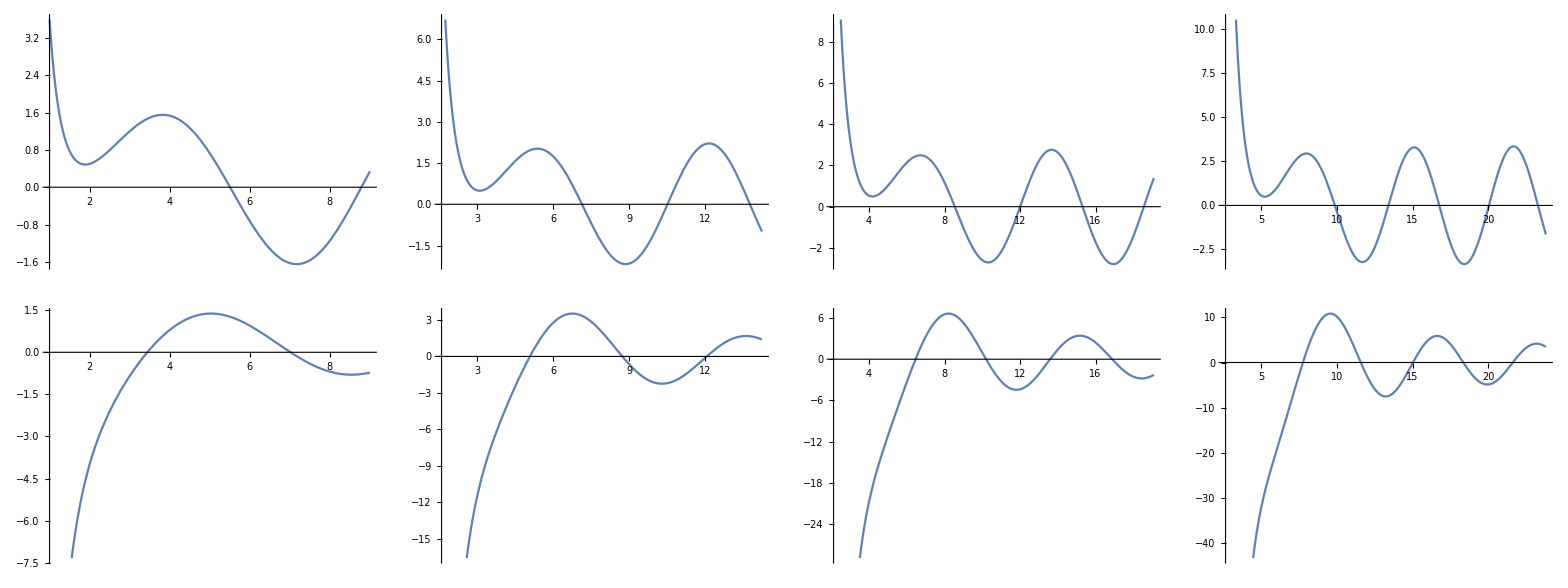

```mathematica
Grid[{
Table[plt[radial][sln[Generic][2,3][l]],{l,2,5}],
Table[plt[radial][sln[Generic][1,3][l]],{l,2,5}]
},Frame->All]
```

#### Нечетные моды (общий вид)

```mathematica
sln[Generic][Odd][l0_]:=Module[{f23=sln[Generic][2,3][l0]//DecayOp[{Full}],f13=sln[Generic][1,3][l0]//DecayOp[{Full}]},Parameterized[(tha//thmasked[Odd])/.{f[1,3]->(Decay@f13[[1]])[r],f[2,3]->(Decay@f23[[1]])[r]},f23[[2]]]];
```

#### Нечетные моды (плотность и поток энергии)

```mathematica
intern[Generic][Odd][series][3];
```

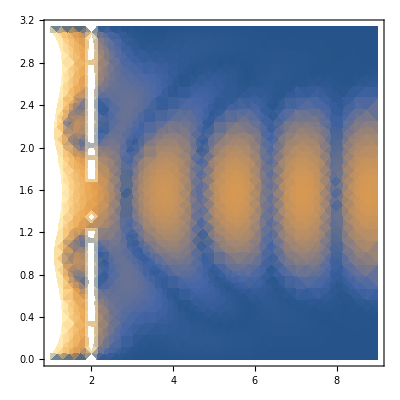
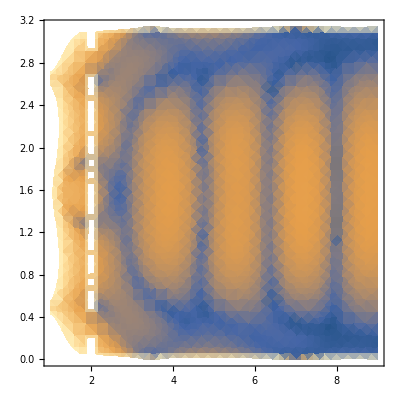
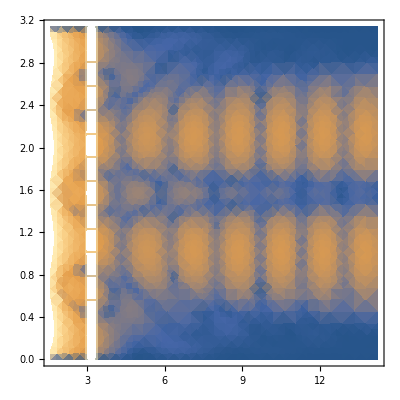
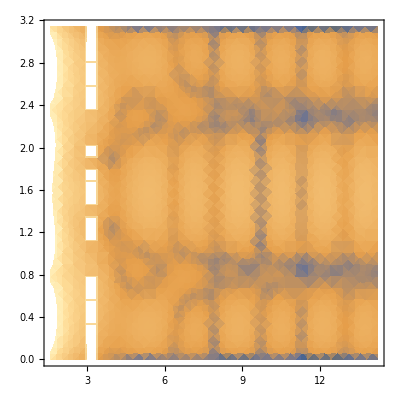

```mathematica
denplt[energy][#,MaxRecursion->2]&/@(cache[Generic][Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})
```

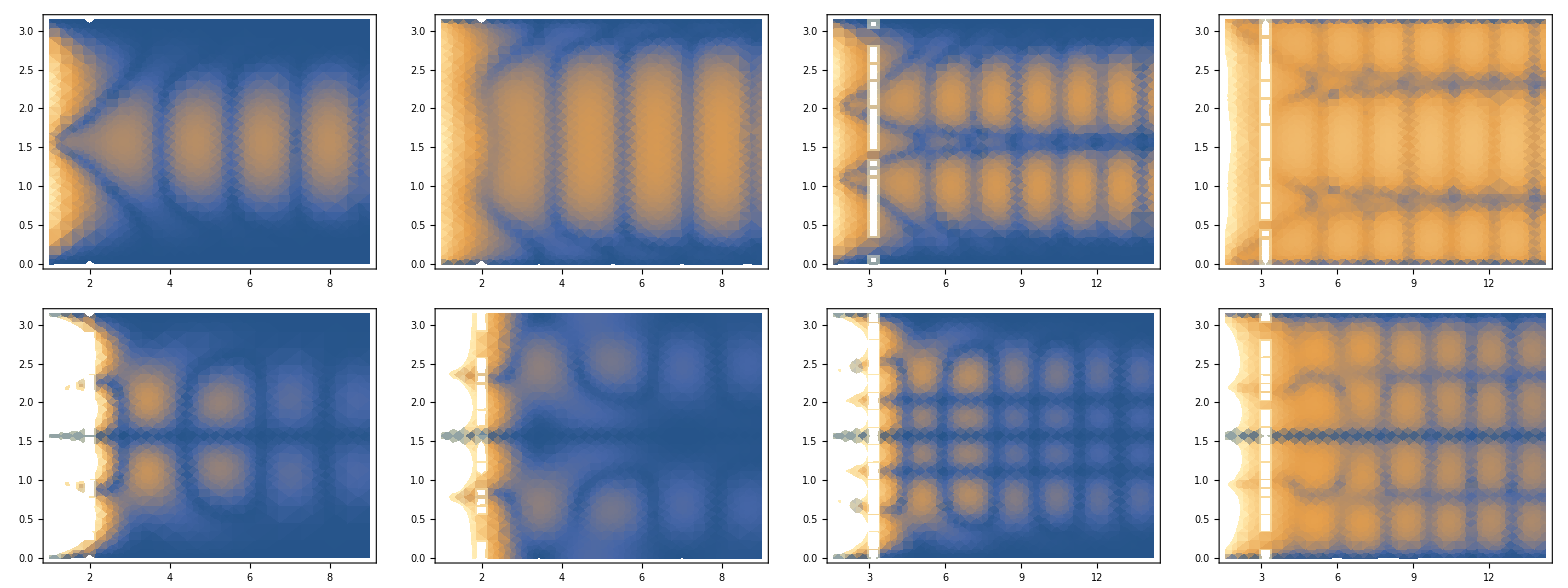

```mathematica
denplt[pointing,{1,2}][#,MaxRecursion->2]&/@(cache[Generic][Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Transpose//Grid
```

#### Нечетные моды (различные соотношения)

```mathematica
intern[Generic][Odd][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]//Decay]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.33]}]/.{u->RandomReal[{0,π}],ct->0}
```

{{{0,0,9.45235×10^-7},{0,0,0.0000303334},{0,0,0.0000381624},{0,0,0.000312304}},{{0,0,-6.93144×10^-8},{0,0,-0.000264188},{0,0,0.0000422194},{0,0,-0.000103811}},{{0,0,-2.68435×10^-7},{0,0,0.0000246532},{0,0,-0.0000261785},{0,0,-0.0000481777}},{{0,0,3.02363×10^-7},{0,0,8.54084×10^-6},{0,0,0.0000521858},{0,0,-0.0000364251}},{{0,0,-1.59341×10^-7},{0,0,-4.75117×10^-6},{0,0,-0.0038851},{0,0,0.0000698734}},{{0,0,7.1667×10^-7},{0,0,3.42652×10^-6},{0,0,-0.000112699},{0,0,0.0000537729}},{{0,0,-6.35372×10^-7},{0,0,6.76267×10^-8},{0,0,-0.0000200221},{0,0,-0.000185643}}}

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]//Decay]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.33]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ct->0}
```

{{{0.2234+0.117066 ⅈ,-1.41422-0.741077 ⅈ,-1.38586+2.64467 ⅈ},{17.5822+3.19865 ⅈ,-2.49167-0.453733 ⅈ,-2.82855+15.5471 ⅈ}},{{0.0416304+0.0218151 ⅈ,-1.50279-0.787492 ⅈ,-1.47265+2.8103 ⅈ},{10.9789+1.99735 ⅈ,-2.4692-0.445431 ⅈ,-2.79607+15.3758 ⅈ}},{{-0.0616885-0.032326 ⅈ,-1.48506-0.778201 ⅈ,-1.45528+2.77715 ⅈ},{6.94033+1.26263 ⅈ,-3.12873-0.56955 ⅈ,-3.55143+19.5207 ⅈ}},{{-0.116484-0.0610399 ⅈ,-1.36231-0.713877 ⅈ,-1.33499+2.5476 ⅈ},{4.27582+0.777882 ⅈ,-4.01361-0.730303 ⅈ,-4.55531+25.0392 ⅈ}},{{-0.139801-0.0732586 ⅈ,-1.14803-0.60159 ⅈ,-1.12501+2.14688 ⅈ},{2.43004+0.442087 ⅈ,-4.84583-0.881515 ⅈ,-5.49949+30.2294 ⅈ}},{{-0.142356-0.0745973 ⅈ,-0.864106-0.452807 ⅈ,-0.846775+1.61592 ⅈ},{1.12201+0.204122 ⅈ,-5.45568-0.992579 ⅈ,-6.19181+34.0347 ⅈ}},{{-0.131457-0.068886 ⅈ,-0.53769-0.281761 ⅈ,-0.526909+1.00551 ⅈ},{0.197606+0.0359496 ⅈ,-5.74155-1.04454 ⅈ,-6.51617+35.8177 ⅈ}}}

### Волны в дальней зоне

#### Нечетные моды (радиальные части)

```mathematica
sln[Far][2,3][l_]:=sde[Far][2,3][l];
sln[Far][1,3][l_][r_]:=0;
```

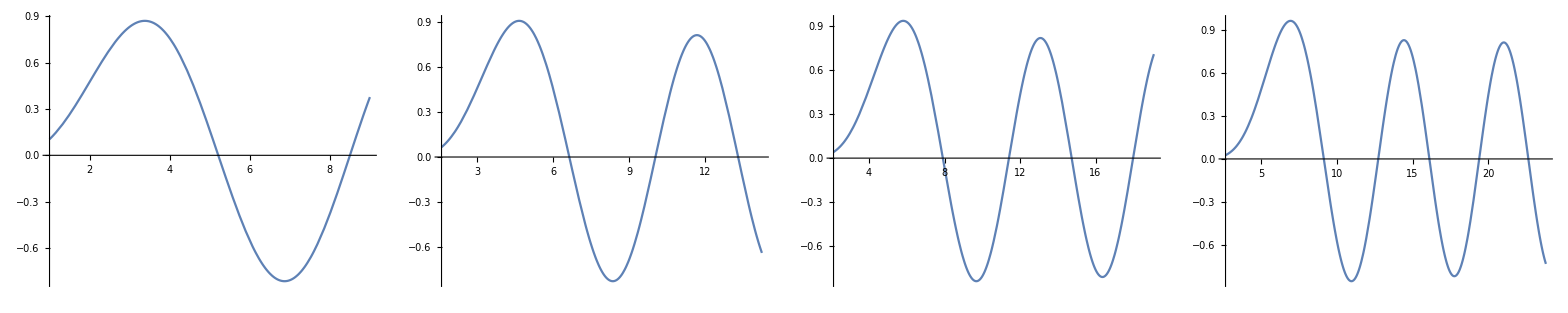

```mathematica
Grid[{
Table[plt[radial][sln[Far][2,3][l]],{l,2,5}]
},Frame->All]
```

#### Нечетные моды (базовые, общий вид)

```mathematica
sln[Far][Odd][l0_]:=Module[{f23=sln[Far][2,3][l0]//DecayOp[{Full}],f13=sln[Far][1,3][l0]//DecayOp[{Full}]},Parameterized[(tha//thmasked[Odd])/.{f[1,3]->(Decay@f13[[1]])[r],f[2,3]->(Decay@f23[[1]])[r]},f23[[2]]]];
```

#### [В процессе] Интерференция двух равнопараметрических нечетных мод

```mathematica
sln[Far][Odd][l][{2,3}]/.r->r-r0;
sln[Far][Odd][l][{2,3}];
Grid[{{Manipulate[DensityPlot[%+%%/.{l->2},{r,0,50},{u,0,π}],{r0,-50,0},{l,2,10,1}],
Manipulate[DensityPlot[%+%%/.{l->2},{r,1000,1050},{u,0,π},MaxRecursion->3],{r0,1000-50,1000},{l,2,10,1}]}}]
```

|

#### [В процессе] Плотность энергии нечетных мод с разными L

```mathematica
intern[Far][Odd][series][3];
```

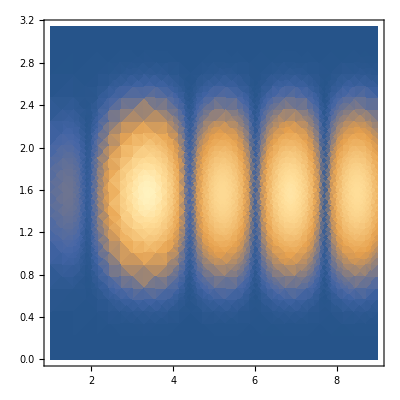
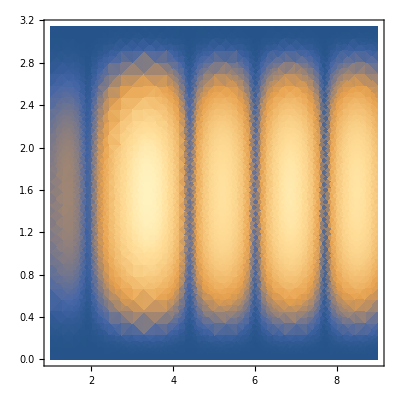
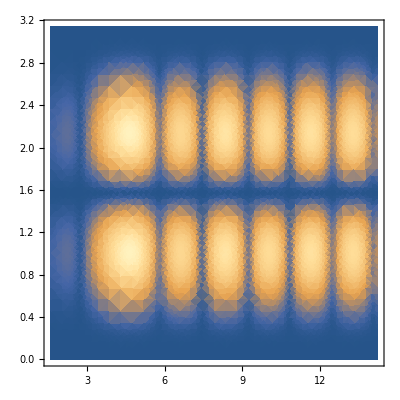
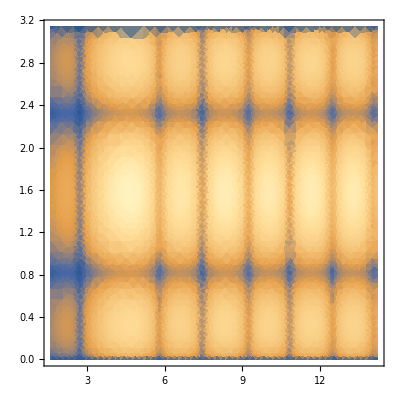

```mathematica
denplt[energy][#,MaxRecursion->3]&/@(cache[Far][Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})
```

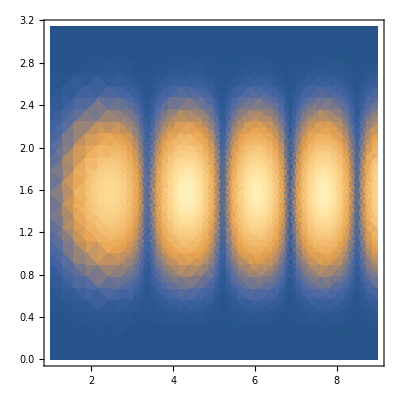
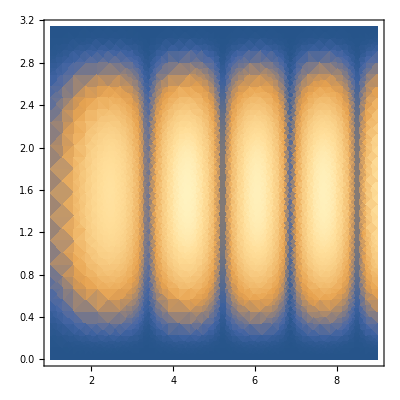
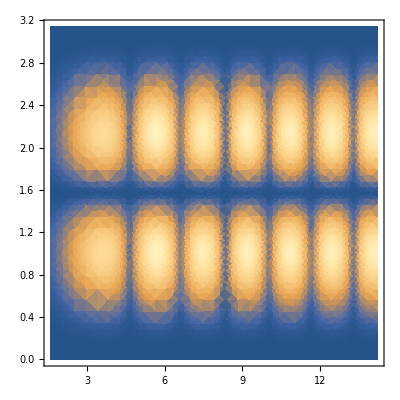
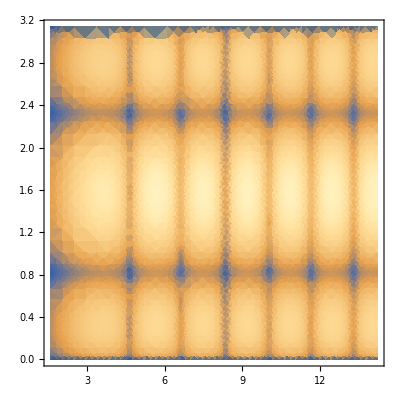

```mathematica
denplt[pointing,1][#,MaxRecursion->3]&/@(cache[Far][Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})
```